```mathematica
SetOptions[Graphics,BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];

SetOptions[{Plot,ListPlot,ParametricPlot},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
```

# Set - Up

## Trade - offs

```mathematica
(* Baseline transformed traits (no care)*)
muStar[params_]:=(θ/. params);
rStar[params_]:=(s*Exp[-(1-θ)])/. params;
nuStar[params_]:=(1-(1-ν0)*Exp[-(1-θ)])/. params;
sigmaJStar[params_]:=(1-(1-σJ0)*Exp[-(1-θ)])/. params;

(* Exponential trade-off*)
tradeOff["Exp"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
{mu0*Exp[-a*c],r0*Exp[-c],1-(1-nu0b)*Exp[-c],1-(1-sigmaJ0b)*Exp[-a*c]}/. params];

(* Saturating trade-off*)
tradeOff["Saturating"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b,V=0.9,Khalf=0.3,sigmaJMax=0.9,costR=0.8,costNu=0.8},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
{mu0*(1-(V*c)/(Khalf+c)),r0*Exp[-costR*c],1-(1-nu0b)*Exp[-costNu*c],sigmaJ0b+(sigmaJMax-sigmaJ0b)*(c/(Khalf+c))}/. params];

(* Sigmoid trade-off*)
tradeOff["Sigmoid"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b,k=10.,c0=0.3,sigmaJMax=1,L,L0,Lnorm},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
L[x_]:=1/(1+Exp[-k*(x-c0)]);
L0=L[0];
Lnorm[x_]:=(L[x]-L0)/(1-L0);
{mu0*(1-L[c]),r0*Exp[-c],1-(1-nu0b)*Exp[-c],sigmaJ0b+(sigmaJMax-sigmaJ0b)*Lnorm[c]}/. params];
```

## Optimal Parameters

```mathematica
(* Optimal parameters from deterministic analysis*)
baseParamsJuvenile={θ->0.8,ν0->0.1,s->6,mE->0.2,K->250,a->6};

meanSJ=0.323823;
careVals=Range[0,2,0.02];
```

## Juvenile Survival Distribution

```mathematica
juvenileSurvivalDist[mean_,kappa_]:=Module[{alpha,beta},alpha=mean*kappa;
beta=(1-mean)*kappa;
BetaDistribution[alpha,beta]];
```

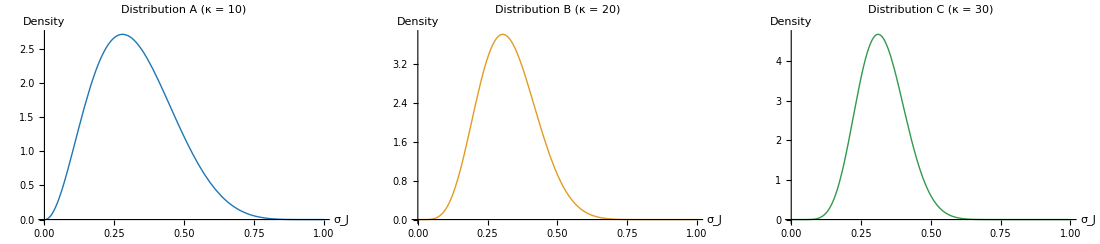

```mathematica
meanSJ=0.323823;
kappaVals={10,20,30};

cols={RGBColor[0.121,0.467,0.705],RGBColor[0.881,0.611,0.142],RGBColor[0.2,0.6,0.3]};

labels={"A","B","C"};

plots=Table[Module[{alpha,beta,dist},alpha=meanSJ*kappaVals[[i]];
beta=(1-meanSJ)*kappaVals[[i]];
dist=BetaDistribution[alpha,beta];
Plot[PDF[dist,x],{x,0,1},PlotStyle->Directive[cols[[i]],Thick],PlotRange->All,Axes->True,AxesOrigin->{0,0},AxesLabel->{Subscript[σ,"J"],"Density"},TicksStyle->Directive[Black,12],LabelStyle->Directive[Black,14],PlotTheme->"Classic",PlotLabel->Style[Row[{"Distribution ",labels[[i]]," (κ = ",kappaVals[[i]],")"}],18],ImageSize->350]],{i,1,3}];

distFigure=GraphicsRow[plots,Spacings->20,ImageSize->1100];

distFigure
```

## Functions

```mathematica
getFitFixedC[params_,shape_String:"Exp"]:=Module[{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
(*resident:no care*)
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
(*mutant:fixed care c=0.5*)
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,0.5];
(*resident equilibrium*)
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
(*invasion Jacobian*)
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
(*dominant eigenvalue*)
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//N//Re;
V];

getFitAtC[params_,c_,shape_String:"Exp"]:=Module[{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
(*resident:no care*)
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
(*mutant:care=c*)
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,c];
(*resident equilibrium*)
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
(*invasion Jacobian*)
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
(*dominant eigenvalue*)
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//N//Re;
V];
```

## Big Function

```mathematica
runJuvenileSurvivalCase[kappa_,n_,seed_,shape_String:"Exp"]:=Module[
{sjVals,(*sampled juvenile survival values*)
paramSets,(*full parameter sets with different juvenile survival*)
fitnessFixedC,(*invasion fitness at fixed care c=0.5*)
resultsFixedC,(*paired (juvenile survival x fitness) values*)
fitnessByCare,(*invasion fitness across care*)
meanByCare,(*mean fitness across care*)
sdByCare          (*standard deviation across care*)},

(*fix the seed*)
SeedRandom[seed];

(*draw n juvenile survival values*)
sjVals=RandomVariate[juvenileSurvivalDist[meanSJ,kappa],n];

(*plot the sampled juvenile survival distribution*)Print[Histogram[sjVals,20,AxesLabel->{"Juvenile survival (σJ0)","Frequency"},PlotLabel->"Juvenile survival distribution ("<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

(*build full parameter sets by replacing juvenile survival*)
paramSets=Table[Join[baseParamsJuvenile,{σJ0->sj}],{sj,sjVals}];

(*caluclate invasion fitness at fixed care*)
fitnessFixedC=Table[getFitFixedC[paramSets[[i]],shape],{i,Length[paramSets]}];

(*pair juvenile survival values with fitness*)
resultsFixedC=Transpose[{sjVals,fitnessFixedC}];

(*plot fitness vs juvenile survival at c=0.5*)Print[ListPlot[resultsFixedC,AxesLabel->{"Juvenile survival (σJ0)","Fitness (λ)"},PlotRange->All,PlotLabel->"Fitness vs juvenile survival ("<>shape<>", c = 0.5, κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

(*do invasion fitness across care*)
fitnessByCare=Table[{c,Table[getFitAtC[paramSets[[i]],c,shape],{i,Length[paramSets]}]},{c,careVals}];

(* calculate mean fitness across care*)
meanByCare={#[[1]],Mean[#[[2]]]}&/@fitnessByCare;

(*SD of fitness across care*)
sdByCare={#[[1]],StandardDeviation[#[[2]]]}&/@fitnessByCare;

(*plot mean fitness vs care*)Print[ListPlot[meanByCare,Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotRange->All,PlotLabel->"Mean fitness vs care ("<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

(*plot SD of fitness vs care*)Print[ListPlot[sdByCare,Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotRange->All,PlotLabel->"SD of fitness vs care ("<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

{meanByCare,sdByCare}];
```

# Exponential

## Bulk Code

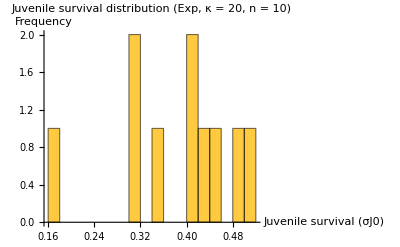

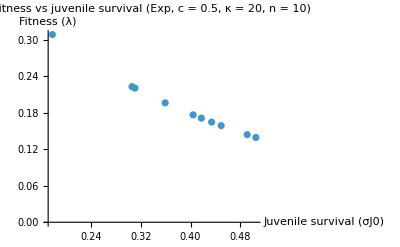

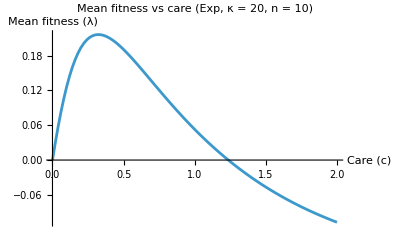

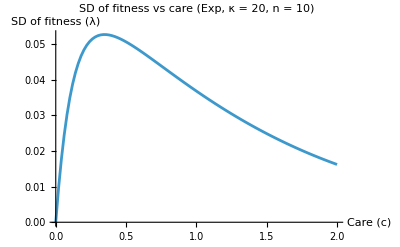

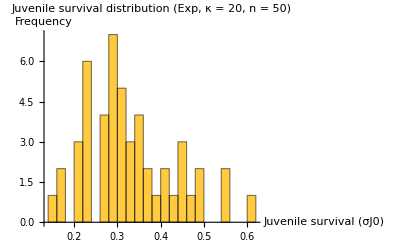

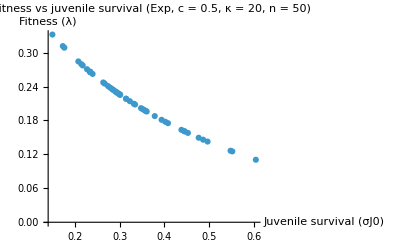

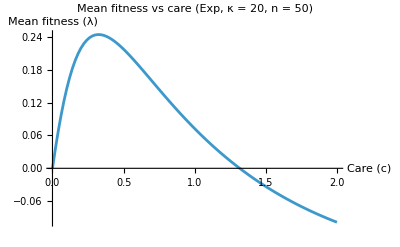

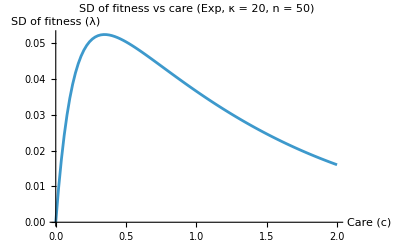

```mathematica
{meanFitnessByCareSJA10Exp,sdFitnessByCareSJA10Exp}=runJuvenileSurvivalCase[20,10,2010,"Exp"];

{meanFitnessByCareSJA50Exp,sdFitnessByCareSJA50Exp}=runJuvenileSurvivalCase[20,50,2050,"Exp"];

{meanFitnessByCareSJA100Exp,sdFitnessByCareSJA100Exp}=runJuvenileSurvivalCase[20,100,2100,"Exp"];


{meanFitnessByCareSJB10Exp,sdFitnessByCareSJB10Exp}=runJuvenileSurvivalCase[10,10,1010,"Exp"];

{meanFitnessByCareSJB50Exp,sdFitnessByCareSJB50Exp}=runJuvenileSurvivalCase[10,50,1050,"Exp"];

{meanFitnessByCareSJB100Exp,sdFitnessByCareSJB100Exp}=runJuvenileSurvivalCase[10,100,1100,"Exp"];


{meanFitnessByCareSJC10Exp,sdFitnessByCareSJC10Exp}=runJuvenileSurvivalCase[30,10,3010,"Exp"];

{meanFitnessByCareSJC50Exp,sdFitnessByCareSJC50Exp}=runJuvenileSurvivalCase[30,50,3050,"Exp"];

{meanFitnessByCareSJC100Exp,sdFitnessByCareSJC100Exp}=runJuvenileSurvivalCase[30,100,3100,"Exp"];
```

```mathematica
meanLambda=Mean[fitnessFixedC];
sdLambda=StandardDeviation[fitnessFixedC];
```

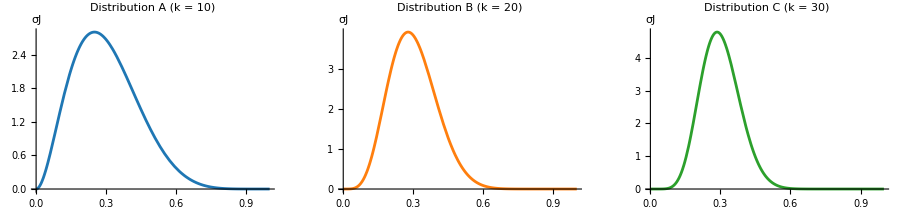

```mathematica
meanSJ=0.3;

alpha[mean_,k_]:=mean*k;
beta[mean_,k_]:=(1-mean)*k;

distA=BetaDistribution[alpha[meanSJ,10],beta[meanSJ,10]];
distB=BetaDistribution[alpha[meanSJ,20],beta[meanSJ,20]];
distC=BetaDistribution[alpha[meanSJ,30],beta[meanSJ,30]];

plotA=Plot[PDF[distA,x],{x,0,1},PlotStyle->RGBColor[0.121,0.467,0.705],PlotLabel->"Distribution A (k = 10)",AxesLabel->{"","σJ"},LabelStyle->Directive[FontFamily->"Times New Roman",12],TicksStyle->Directive[FontFamily->"Times New Roman",10],PlotRange->All];

plotB=Plot[PDF[distB,x],{x,0,1},PlotStyle->RGBColor[1.0,0.498,0.0549],PlotLabel->"Distribution B (k = 20)",AxesLabel->{"","σJ"},LabelStyle->Directive[FontFamily->"Times New Roman",12],TicksStyle->Directive[FontFamily->"Times New Roman",10],PlotRange->All];

plotC=Plot[PDF[distC,x],{x,0,1},PlotStyle->RGBColor[0.172,0.627,0.172],PlotLabel->"Distribution C (k = 30)",AxesLabel->{"","σJ"},LabelStyle->Directive[FontFamily->"Times New Roman",12],TicksStyle->Directive[FontFamily->"Times New Roman",10],PlotRange->All];

GraphicsRow[{plotA,plotB,plotC},ImageSize->900]
```

## Plot for Figure

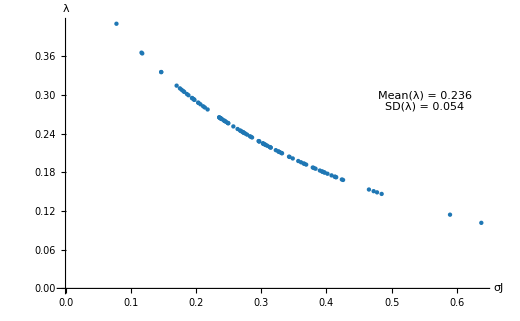

```mathematica
SeedRandom[2100];

sjVals=RandomVariate[juvenileSurvivalDist[meanSJ,20],100];

paramSets=Table[Join[baseParamsJuvenile,{σJ0->sj}],{sj,sjVals}];

fitnessFixedC=Table[getFitFixedC[paramSets[[i]],"Exp"],{i,Length[paramSets]}];

resultsFixedC=Transpose[{sjVals,fitnessFixedC}];

meanLambda=Mean[fitnessFixedC];
sdLambda=StandardDeviation[fitnessFixedC];

distPlot=ListPlot[resultsFixedC,PlotStyle->Directive[RGBColor[0.121,0.467,0.705],PointSize[0.006]],Axes->True,AxesOrigin->{0,0},AxesLabel->{"σJ","λ"},TicksStyle->Directive[Black,12,FontFamily->"Times New Roman"],LabelStyle->Directive[Black,14,FontFamily->"Times New Roman"],PlotTheme->"Classic",PlotRange->All,ImageSize->520,ImagePadding->{{80,150},{60,80}},PlotRangeClipping->False,Epilog->{Inset[Column[{Style[Row[{"Mean(λ) = ",NumberForm[meanLambda,{3,3}]}],18,Orange,FontFamily->"Times New Roman"],Style[Row[{"SD(λ) = ",NumberForm[sdLambda,{3,3}]}],18,RGBColor[0,0.35,0],FontFamily->"Times New Roman"]},Spacings->0.4],Scaled[{0.85,0.7}]]}];

distPlot
```

## Diagnostic Plots

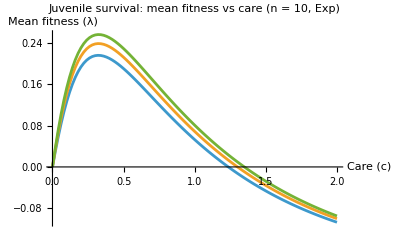

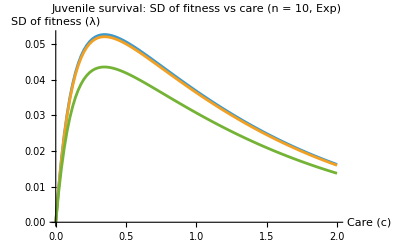

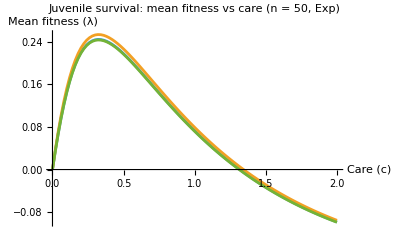

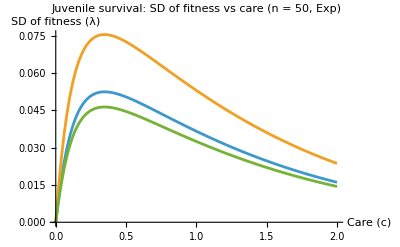

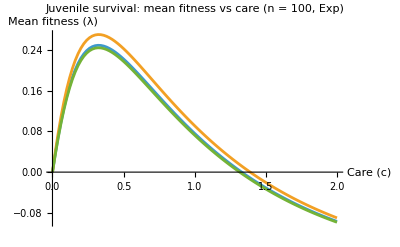

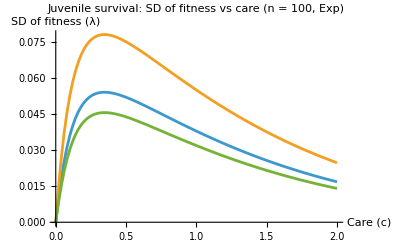

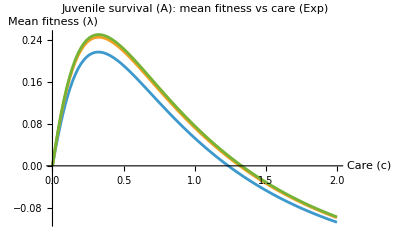

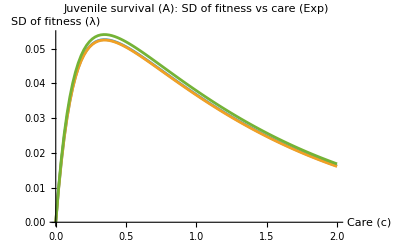

```mathematica
(*Grouped by sample size*)

ListPlot[{meanFitnessByCareSJA10Exp,meanFitnessByCareSJB10Exp,meanFitnessByCareSJC10Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: mean fitness vs care (n = 10, Exp)"]

ListPlot[{sdFitnessByCareSJA10Exp,sdFitnessByCareSJB10Exp,sdFitnessByCareSJC10Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: SD of fitness vs care (n = 10, Exp)"]


ListPlot[{meanFitnessByCareSJA50Exp,meanFitnessByCareSJB50Exp,meanFitnessByCareSJC50Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: mean fitness vs care (n = 50, Exp)"]

ListPlot[{sdFitnessByCareSJA50Exp,sdFitnessByCareSJB50Exp,sdFitnessByCareSJC50Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: SD of fitness vs care (n = 50, Exp)"]


ListPlot[{meanFitnessByCareSJA100Exp,meanFitnessByCareSJB100Exp,meanFitnessByCareSJC100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: mean fitness vs care (n = 100, Exp)"]

ListPlot[{sdFitnessByCareSJA100Exp,sdFitnessByCareSJB100Exp,sdFitnessByCareSJC100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: SD of fitness vs care (n = 100, Exp)"]

(*Grouped by distribution*)

ListPlot[{meanFitnessByCareSJA10Exp,meanFitnessByCareSJA50Exp,meanFitnessByCareSJA100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (A): mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareSJA10Exp,sdFitnessByCareSJA50Exp,sdFitnessByCareSJA100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (A): SD of fitness vs care (Exp)"]


ListPlot[{meanFitnessByCareSJB10Exp,meanFitnessByCareSJB50Exp,meanFitnessByCareSJB100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (B): mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareSJB10Exp,sdFitnessByCareSJB50Exp,sdFitnessByCareSJB100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (B): SD of fitness vs care (Exp)"]


ListPlot[{meanFitnessByCareSJC10Exp,meanFitnessByCareSJC50Exp,meanFitnessByCareSJC100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (C): mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareSJC10Exp,sdFitnessByCareSJC50Exp,sdFitnessByCareSJC100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (C): SD of fitness vs care (Exp)"]
```

## Tables

## Mean

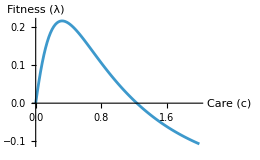
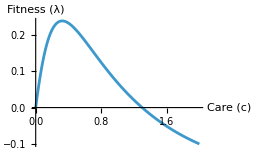
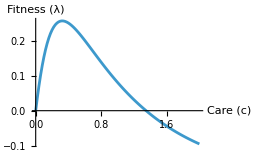
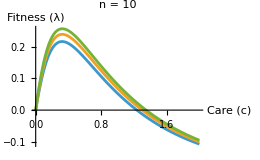
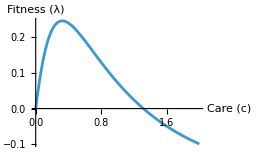
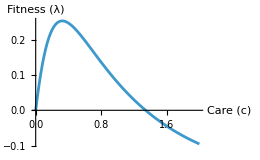
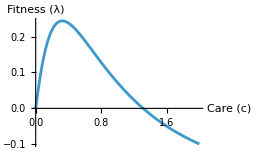
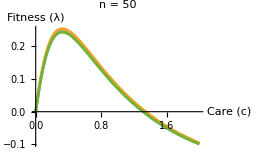
Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
plotOpts={Joined->True,PlotRange->All,AxesLabel->{"Care (c)","Fitness (λ)"},ImageSize->260};

meanA10=ListPlot[{meanFitnessByCareSJA10Exp,meanFitnessByCareSJB10Exp,meanFitnessByCareSJC10Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanA50=ListPlot[{meanFitnessByCareSJA50Exp,meanFitnessByCareSJB50Exp,meanFitnessByCareSJC50Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanA100=ListPlot[{meanFitnessByCareSJA100Exp,meanFitnessByCareSJB100Exp,meanFitnessByCareSJC100Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanCompA=ListPlot[{meanFitnessByCareSJA10Exp,meanFitnessByCareSJA50Exp,meanFitnessByCareSJA100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanCompB=ListPlot[{meanFitnessByCareSJB10Exp,meanFitnessByCareSJB50Exp,meanFitnessByCareSJB100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanCompC=ListPlot[{meanFitnessByCareSJC10Exp,meanFitnessByCareSJC50Exp,meanFitnessByCareSJC100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];

meanTable=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareSJA10Exp},plotOpts],ListPlot[{meanFitnessByCareSJB10Exp},plotOpts],ListPlot[{meanFitnessByCareSJC10Exp},plotOpts],meanA10},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareSJA50Exp},plotOpts],ListPlot[{meanFitnessByCareSJB50Exp},plotOpts],ListPlot[{meanFitnessByCareSJC50Exp},plotOpts],meanA50},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareSJA100Exp},plotOpts],ListPlot[{meanFitnessByCareSJB100Exp},plotOpts],ListPlot[{meanFitnessByCareSJC100Exp},plotOpts],meanA100},{Style["Compiled",Bold],meanCompA,meanCompB,meanCompC,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];
meanTable
```

```mathematica
plotOpts={Joined->True,PlotRange->All,AxesLabel->{"Care (c)","Fitness (λ)"},ImageSize->260};

meanA10=ListPlot[{meanFitnessByCareSJA10Exp,meanFitnessByCareSJB10Exp,meanFitnessByCareSJC10Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",Evaluate[plotOpts]];

meanA50=ListPlot[{meanFitnessByCareSJA50Exp,meanFitnessByCareSJB50Exp,meanFitnessByCareSJC50Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",Evaluate[plotOpts]];

meanA100=ListPlot[{meanFitnessByCareSJA100Exp,meanFitnessByCareSJB100Exp,meanFitnessByCareSJC100Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",Evaluate[plotOpts]];

meanCompA=ListPlot[{meanFitnessByCareSJA10Exp,meanFitnessByCareSJA50Exp,meanFitnessByCareSJA100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",Evaluate[plotOpts]];

meanCompB=ListPlot[{meanFitnessByCareSJB10Exp,meanFitnessByCareSJB50Exp,meanFitnessByCareSJB100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",Evaluate[plotOpts]];

meanCompC=ListPlot[{meanFitnessByCareSJC10Exp,meanFitnessByCareSJC50Exp,meanFitnessByCareSJC100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",Evaluate[plotOpts]];

meanTable=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareSJA10Exp},Evaluate[plotOpts]],ListPlot[{meanFitnessByCareSJB10Exp},Evaluate[plotOpts]],ListPlot[{meanFitnessByCareSJC10Exp},Evaluate[plotOpts]],meanA10},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareSJA50Exp},Evaluate[plotOpts]],ListPlot[{meanFitnessByCareSJB50Exp},Evaluate[plotOpts]],ListPlot[{meanFitnessByCareSJC50Exp},Evaluate[plotOpts]],meanA50},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareSJA100Exp},Evaluate[plotOpts]],ListPlot[{meanFitnessByCareSJB100Exp},Evaluate[plotOpts]],ListPlot[{meanFitnessByCareSJC100Exp},Evaluate[plotOpts]],meanA100},{Style["Compiled",Bold],meanCompA,meanCompB,meanCompC,Graphics[{},ImageSize->260]}},Frame->All,Spacings->{2,2},Alignment->Center,Background->White];

meanTableImage=Rasterize[meanTable,"Image",ImageResolution->300];

meanTableImage
```

-Graphics-

-Graphics-

```mathematica
plotOpts={Joined->True,PlotRange->All,PlotStyle->Orange,AxesLabel->{"Care (c)","Fitness (λ)"},ImageSize->260};

meanTable9=Rasterize[Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareSJA10Exp},Evaluate@plotOpts],ListPlot[{meanFitnessByCareSJB10Exp},Evaluate@plotOpts],ListPlot[{meanFitnessByCareSJC10Exp},Evaluate@plotOpts]},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareSJA50Exp},Evaluate@plotOpts],ListPlot[{meanFitnessByCareSJB50Exp},Evaluate@plotOpts],ListPlot[{meanFitnessByCareSJC50Exp},Evaluate@plotOpts]},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareSJA100Exp},Evaluate@plotOpts],ListPlot[{meanFitnessByCareSJB100Exp},Evaluate@plotOpts],ListPlot[{meanFitnessByCareSJC100Exp},Evaluate@plotOpts]}},Frame->All,Spacings->{2,2},Alignment->Center],"Image",ImageResolution->300];

meanTable9
```

-Graphics-

## SD

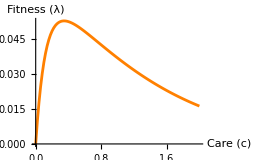
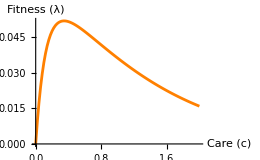
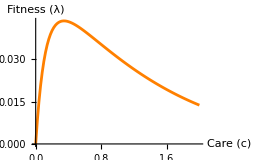
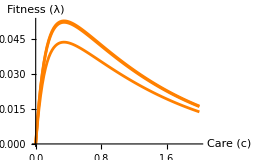
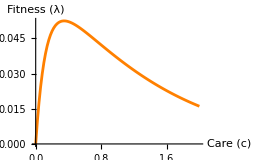
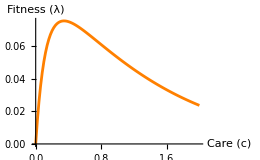
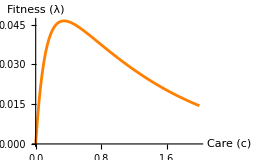
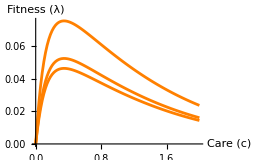
SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
sdTable=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareSJA10Exp},plotOpts],ListPlot[{sdFitnessByCareSJB10Exp},plotOpts],ListPlot[{sdFitnessByCareSJC10Exp},plotOpts],ListPlot[{sdFitnessByCareSJA10Exp,sdFitnessByCareSJB10Exp,sdFitnessByCareSJC10Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareSJA50Exp},plotOpts],ListPlot[{sdFitnessByCareSJB50Exp},plotOpts],ListPlot[{sdFitnessByCareSJC50Exp},plotOpts],ListPlot[{sdFitnessByCareSJA50Exp,sdFitnessByCareSJB50Exp,sdFitnessByCareSJC50Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareSJA100Exp},plotOpts],ListPlot[{sdFitnessByCareSJB100Exp},plotOpts],ListPlot[{sdFitnessByCareSJC100Exp},plotOpts],ListPlot[{sdFitnessByCareSJA100Exp,sdFitnessByCareSJB100Exp,sdFitnessByCareSJC100Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareSJA10Exp,sdFitnessByCareSJA50Exp,sdFitnessByCareSJA100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareSJB10Exp,sdFitnessByCareSJB50Exp,sdFitnessByCareSJB100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareSJC10Exp,sdFitnessByCareSJC50Exp,sdFitnessByCareSJC100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];
sdTable
```

```mathematica
sdPlotOpts={Joined->True,PlotRange->All,AxesLabel->{"Care (c)","SD of Fitness"},ImageSize->260};

sdA10=ListPlot[{sdFitnessByCareSJA10Exp,sdFitnessByCareSJB10Exp,sdFitnessByCareSJC10Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",sdPlotOpts];

sdA50=ListPlot[{sdFitnessByCareSJA50Exp,sdFitnessByCareSJB50Exp,sdFitnessByCareSJC50Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",sdPlotOpts];

sdA100=ListPlot[{sdFitnessByCareSJA100Exp,sdFitnessByCareSJB100Exp,sdFitnessByCareSJC100Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",sdPlotOpts];

sdCompA=ListPlot[{sdFitnessByCareSJA10Exp,sdFitnessByCareSJA50Exp,sdFitnessByCareSJA100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",sdPlotOpts];

sdCompB=ListPlot[{sdFitnessByCareSJB10Exp,sdFitnessByCareSJB50Exp,sdFitnessByCareSJB100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",sdPlotOpts];

sdCompC=ListPlot[{sdFitnessByCareSJC10Exp,sdFitnessByCareSJC50Exp,sdFitnessByCareSJC100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",sdPlotOpts];

sdTable=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareSJA10Exp},sdPlotOpts],ListPlot[{sdFitnessByCareSJB10Exp},sdPlotOpts],ListPlot[{sdFitnessByCareSJC10Exp},sdPlotOpts],sdA10},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareSJA50Exp},sdPlotOpts],ListPlot[{sdFitnessByCareSJB50Exp},sdPlotOpts],ListPlot[{sdFitnessByCareSJC50Exp},sdPlotOpts],sdA50},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareSJA100Exp},sdPlotOpts],ListPlot[{sdFitnessByCareSJB100Exp},sdPlotOpts],ListPlot[{sdFitnessByCareSJC100Exp},sdPlotOpts],sdA100},{Style["Compiled",Bold],sdCompA,sdCompB,sdCompC,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

sdTableImage=Rasterize[sdTable,ImageResolution->300];

sdTableImage
```

-Graphics-

```mathematica
plotOpts={Joined->True,PlotRange->All,PlotStyle->RGBColor[0,0.35,0],AxesLabel->{"Care (c)","Fitness (λ)"},ImageSize->260};

sdTable9=Rasterize[Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareSJA10Exp},Evaluate@plotOpts],ListPlot[{sdFitnessByCareSJB10Exp},Evaluate@plotOpts],ListPlot[{sdFitnessByCareSJC10Exp},Evaluate@plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareSJA50Exp},Evaluate@plotOpts],ListPlot[{sdFitnessByCareSJB50Exp},Evaluate@plotOpts],ListPlot[{sdFitnessByCareSJC50Exp},Evaluate@plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareSJA100Exp},Evaluate@plotOpts],ListPlot[{sdFitnessByCareSJB100Exp},Evaluate@plotOpts],ListPlot[{sdFitnessByCareSJC100Exp},Evaluate@plotOpts]}},Frame->All,Spacings->{2,2},Alignment->Center],"Image",ImageResolution->300];

sdTable9
```

-Graphics-

## Mean Plots

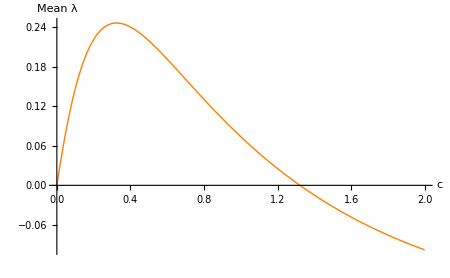

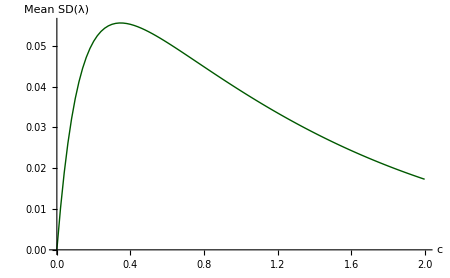

```mathematica
(*Collect all mean curves*)allMeanCurvesSJExp={meanFitnessByCareSJA10Exp,meanFitnessByCareSJA50Exp,meanFitnessByCareSJA100Exp,meanFitnessByCareSJB10Exp,meanFitnessByCareSJB50Exp,meanFitnessByCareSJB100Exp,meanFitnessByCareSJC10Exp,meanFitnessByCareSJC50Exp,meanFitnessByCareSJC100Exp};

(*Collect all SD curves*)
allSDCurvesSJExp={sdFitnessByCareSJA10Exp,sdFitnessByCareSJA50Exp,sdFitnessByCareSJA100Exp,sdFitnessByCareSJB10Exp,sdFitnessByCareSJB50Exp,sdFitnessByCareSJB100Exp,sdFitnessByCareSJC10Exp,sdFitnessByCareSJC50Exp,sdFitnessByCareSJC100Exp};

careValuesSJExp=allMeanCurvesSJExp[[1]][[All,1]];

(*Compute overall mean of means*)
overallMeanSJExp=Transpose[{careValuesSJExp,Mean/@Transpose[allMeanCurvesSJExp[[All,All,2]]]}];

(*Compute overall mean of SDs*)
overallSDSJExp=Transpose[{careValuesSJExp,Mean/@Transpose[allSDCurvesSJExp[[All,All,2]]]}];

(*Plot overall mean*)
plotOverallMeanSJExp=ListPlot[overallMeanSJExp,Joined->True,PlotStyle->Directive[Orange,Thick],PlotRange->All,AxesLabel->{"c","Mean λ"},ImageSize->{450,276}];

(*Plot overall SD*)
plotOverallSDSJExp=ListPlot[overallSDSJExp,Joined->True,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],PlotRange->All,AxesLabel->{"c","Mean SD(λ)"},ImageSize->{450,276}];

plotOverallMeanSJExp
plotOverallSDSJExp
```

## Plot for Figure

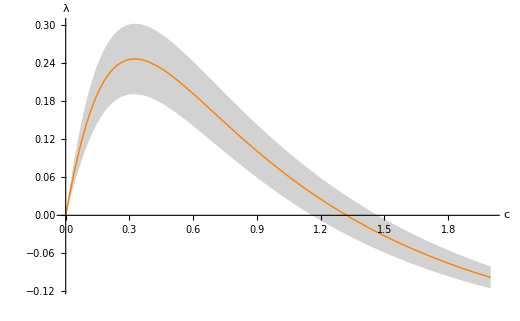

```mathematica
careVals=overallMeanSJExp[[All,1]];
meanVals=overallMeanSJExp[[All,2]];
sdVals=overallSDSJExp[[All,2]];

upper=Transpose[{careVals,meanVals+sdVals}];
lower=Transpose[{careVals,meanVals-sdVals}];

meanWithBandPlot=ListLinePlot[{upper,lower,overallMeanSJExp},Joined->True,PlotRange->All,Filling->{1->{2}},FillingStyle->Directive[GrayLevel[0.75],Opacity[0.7]],PlotStyle->{Directive[Opacity[0]],Directive[Opacity[0]],Directive[Orange,Thick]           },Axes->True,AxesOrigin->{0,0},AxesLabel->{"c","λ"},TicksStyle->Directive[Black,12],LabelStyle->Directive[Black,14],PlotTheme->"Classic",ImageSize->520];

meanWithBandPlot
```

# Saturating

## Bulk Code

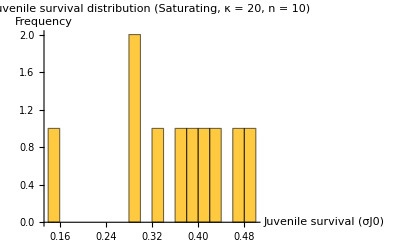

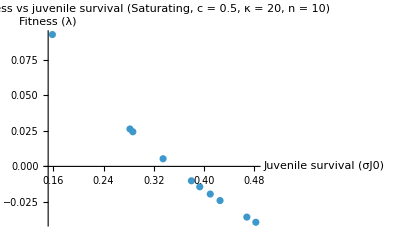

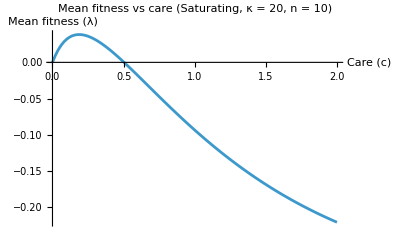

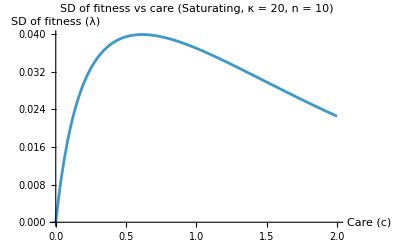

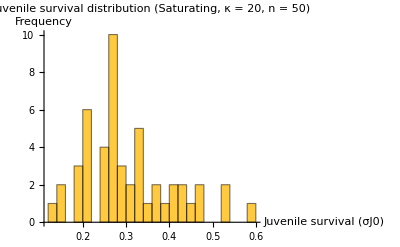

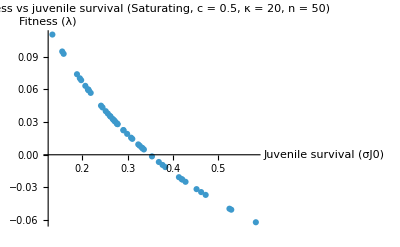

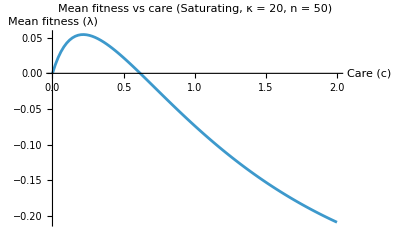

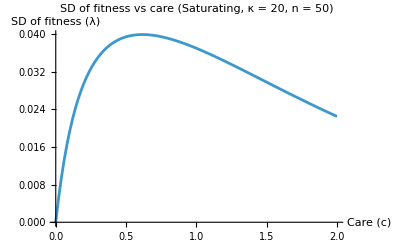

```mathematica
{meanFitnessByCareSJA10Sat,sdFitnessByCareSJA10Sat}=runJuvenileSurvivalCase[20,10,2010,"Saturating"];

{meanFitnessByCareSJA50Sat,sdFitnessByCareSJA50Sat}=runJuvenileSurvivalCase[20,50,2050,"Saturating"];

{meanFitnessByCareSJA100Sat,sdFitnessByCareSJA100Sat}=runJuvenileSurvivalCase[20,100,2100,"Saturating"];


{meanFitnessByCareSJB10Sat,sdFitnessByCareSJB10Sat}=runJuvenileSurvivalCase[10,10,1010,"Saturating"];

{meanFitnessByCareSJB50Sat,sdFitnessByCareSJB50Sat}=runJuvenileSurvivalCase[10,50,1050,"Saturating"];

{meanFitnessByCareSJB100Sat,sdFitnessByCareSJB100Sat}=runJuvenileSurvivalCase[10,100,1100,"Saturating"];


{meanFitnessByCareSJC10Sat,sdFitnessByCareSJC10Sat}=runJuvenileSurvivalCase[30,10,3010,"Saturating"];

{meanFitnessByCareSJC50Sat,sdFitnessByCareSJC50Sat}=runJuvenileSurvivalCase[30,50,3050,"Saturating"];

{meanFitnessByCareSJC100Sat,sdFitnessByCareSJC100Sat}=runJuvenileSurvivalCase[30,100,3100,"Saturating"];
```

## Diagnostic Plots

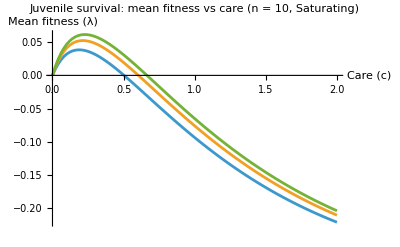

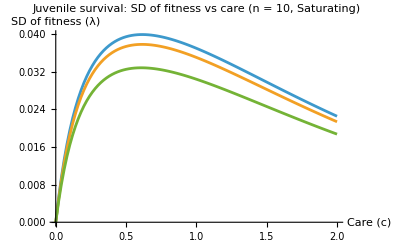

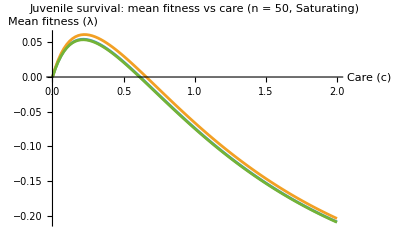

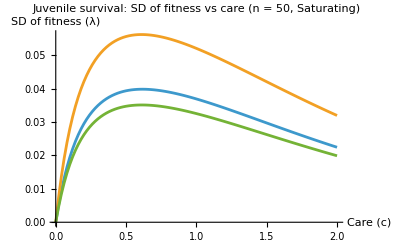

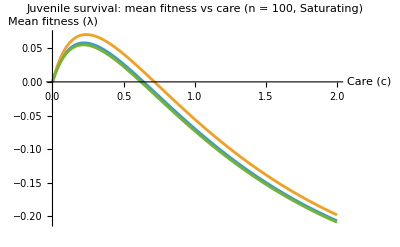

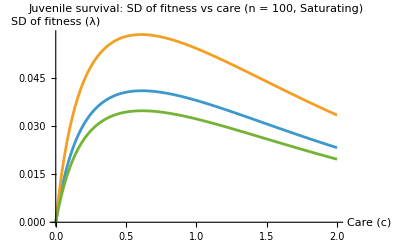

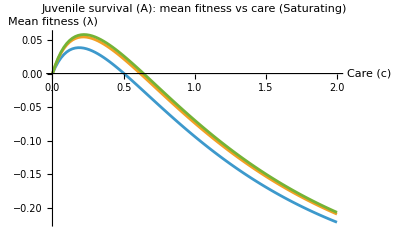

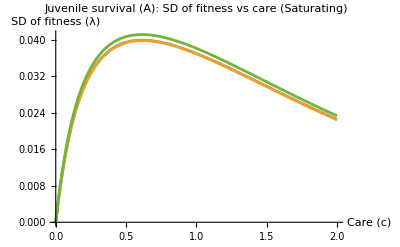

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
(*Grouped by sample size*)
ListPlot[{meanFitnessByCareSJA10Sat,meanFitnessByCareSJB10Sat,meanFitnessByCareSJC10Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: mean fitness vs care (n = 10, Saturating)"]

ListPlot[{sdFitnessByCareSJA10Sat,sdFitnessByCareSJB10Sat,sdFitnessByCareSJC10Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: SD of fitness vs care (n = 10, Saturating)"]


ListPlot[{meanFitnessByCareSJA50Sat,meanFitnessByCareSJB50Sat,meanFitnessByCareSJC50Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: mean fitness vs care (n = 50, Saturating)"]

ListPlot[{sdFitnessByCareSJA50Sat,sdFitnessByCareSJB50Sat,sdFitnessByCareSJC50Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: SD of fitness vs care (n = 50, Saturating)"]


ListPlot[{meanFitnessByCareSJA100Sat,meanFitnessByCareSJB100Sat,meanFitnessByCareSJC100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: mean fitness vs care (n = 100, Saturating)"]

ListPlot[{sdFitnessByCareSJA100Sat,sdFitnessByCareSJB100Sat,sdFitnessByCareSJC100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: SD of fitness vs care (n = 100, Saturating)"]

(*Grouped by distribution*)

ListPlot[{meanFitnessByCareSJA10Sat,meanFitnessByCareSJA50Sat,meanFitnessByCareSJA100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (A): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareSJA10Sat,sdFitnessByCareSJA50Sat,sdFitnessByCareSJA100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (A): SD of fitness vs care (Saturating)"]


ListPlot[{meanFitnessByCareSJB10Sat,meanFitnessByCareSJB50Sat,meanFitnessByCareSJB100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (B): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareSJB10Sat,sdFitnessByCareSJB50Sat,sdFitnessByCareSJB100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (B): SD of fitness vs care (Saturating)"]


ListPlot[{meanFitnessByCareSJC10Sat,meanFitnessByCareSJC50Sat,meanFitnessByCareSJC100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (C): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareSJC10Sat,sdFitnessByCareSJC50Sat,sdFitnessByCareSJC100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (C): SD of fitness vs care (Saturating)"]
```

## Tables

```mathematica
meanA10Sat=ListPlot[{meanFitnessByCareSJA10Sat,meanFitnessByCareSJB10Sat,meanFitnessByCareSJC10Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanA50Sat=ListPlot[{meanFitnessByCareSJA50Sat,meanFitnessByCareSJB50Sat,meanFitnessByCareSJC50Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanA100Sat=ListPlot[{meanFitnessByCareSJA100Sat,meanFitnessByCareSJB100Sat,meanFitnessByCareSJC100Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanCompASat=ListPlot[{meanFitnessByCareSJA10Sat,meanFitnessByCareSJA50Sat,meanFitnessByCareSJA100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanCompBSat=ListPlot[{meanFitnessByCareSJB10Sat,meanFitnessByCareSJB50Sat,meanFitnessByCareSJB100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanCompCSat=ListPlot[{meanFitnessByCareSJC10Sat,meanFitnessByCareSJC50Sat,meanFitnessByCareSJC100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];
meanTableSat=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareSJA10Sat},plotOpts],ListPlot[{meanFitnessByCareSJB10Sat},plotOpts],ListPlot[{meanFitnessByCareSJC10Sat},plotOpts],meanA10Sat},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareSJA50Sat},plotOpts],ListPlot[{meanFitnessByCareSJB50Sat},plotOpts],ListPlot[{meanFitnessByCareSJC50Sat},plotOpts],meanA50Sat},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareSJA100Sat},plotOpts],ListPlot[{meanFitnessByCareSJB100Sat},plotOpts],ListPlot[{meanFitnessByCareSJC100Sat},plotOpts],meanA100Sat},{Style["Compiled",Bold],meanCompASat,meanCompBSat,meanCompCSat,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];
meanTableSat
```

Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
sdTableSat=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareSJA10Sat},plotOpts],ListPlot[{sdFitnessByCareSJB10Sat},plotOpts],ListPlot[{sdFitnessByCareSJC10Sat},plotOpts],ListPlot[{sdFitnessByCareSJA10Sat,sdFitnessByCareSJB10Sat,sdFitnessByCareSJC10Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareSJA50Sat},plotOpts],ListPlot[{sdFitnessByCareSJB50Sat},plotOpts],ListPlot[{sdFitnessByCareSJC50Sat},plotOpts],ListPlot[{sdFitnessByCareSJA50Sat,sdFitnessByCareSJB50Sat,sdFitnessByCareSJC50Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareSJA100Sat},plotOpts],ListPlot[{sdFitnessByCareSJB100Sat},plotOpts],ListPlot[{sdFitnessByCareSJC100Sat},plotOpts],ListPlot[{sdFitnessByCareSJA100Sat,sdFitnessByCareSJB100Sat,sdFitnessByCareSJC100Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareSJA10Sat,sdFitnessByCareSJA50Sat,sdFitnessByCareSJA100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareSJB10Sat,sdFitnessByCareSJB50Sat,sdFitnessByCareSJB100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareSJC10Sat,sdFitnessByCareSJC50Sat,sdFitnessByCareSJC100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];
sdTableSat
```

SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Mean Plots

```mathematica
(*Collect all mean curves*)allMeanCurvesSJSat={meanFitnessByCareSJA10Sat,meanFitnessByCareSJA50Sat,meanFitnessByCareSJA100Sat,meanFitnessByCareSJB10Sat,meanFitnessByCareSJB50Sat,meanFitnessByCareSJB100Sat,meanFitnessByCareSJC10Sat,meanFitnessByCareSJC50Sat,meanFitnessByCareSJC100Sat};

(*Collect all SD curves*)
allSDCurvesSJSat={sdFitnessByCareSJA10Sat,sdFitnessByCareSJA50Sat,sdFitnessByCareSJA100Sat,sdFitnessByCareSJB10Sat,sdFitnessByCareSJB50Sat,sdFitnessByCareSJB100Sat,sdFitnessByCareSJC10Sat,sdFitnessByCareSJC50Sat,sdFitnessByCareSJC100Sat};


careValuesSJSat=allMeanCurvesSJSat[[1]][[All,1]];

(*Compute overall mean of means*)
overallMeanSJSat=Transpose[{careValuesSJSat,Mean/@Transpose[allMeanCurvesSJSat[[All,All,2]]]}];

(*Compute overall mean of SDs*)
overallSDSJSat=Transpose[{careValuesSJSat,Mean/@Transpose[allSDCurvesSJSat[[All,All,2]]]}];

(*Plot overall mean*)
plotOverallMeanSJSat=ListPlot[overallMeanSJSat,Joined->True,PlotRange->All,PlotStyle->Directive[Orange,Thick],AxesLabel->{"c","Mean λ"}];

(*Plot overall SD*)
plotOverallSDSJSat=ListPlot[overallSDSJSat,Joined->True,PlotRange->All,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],AxesLabel->{"c","Mean SD(λ)"}];

plotOverallMeanSJSat
plotOverallSDSJSat
```

-Graphics-

-Graphics-

# Sigmoid

## Bulk Code

```mathematica
{meanFitnessByCareSJA10Sig,sdFitnessByCareSJA10Sig}=runJuvenileSurvivalCase[20,10,2010,"Sigmoid"];

{meanFitnessByCareSJA50Sig,sdFitnessByCareSJA50Sig}=runJuvenileSurvivalCase[20,50,2050,"Sigmoid"];

{meanFitnessByCareSJA100Sig,sdFitnessByCareSJA100Sig}=runJuvenileSurvivalCase[20,100,2100,"Sigmoid"];


{meanFitnessByCareSJB10Sig,sdFitnessByCareSJB10Sig}=runJuvenileSurvivalCase[10,10,1010,"Sigmoid"];

{meanFitnessByCareSJB50Sig,sdFitnessByCareSJB50Sig}=runJuvenileSurvivalCase[10,50,1050,"Sigmoid"];

{meanFitnessByCareSJB100Sig,sdFitnessByCareSJB100Sig}=runJuvenileSurvivalCase[10,100,1100,"Sigmoid"];


{meanFitnessByCareSJC10Sig,sdFitnessByCareSJC10Sig}=runJuvenileSurvivalCase[30,10,3010,"Sigmoid"];

{meanFitnessByCareSJC50Sig,sdFitnessByCareSJC50Sig}=runJuvenileSurvivalCase[30,50,3050,"Sigmoid"];

{meanFitnessByCareSJC100Sig,sdFitnessByCareSJC100Sig}=runJuvenileSurvivalCase[30,100,3100,"Sigmoid"];
```

-Graphics-

-Graphics-

-Graphics-

«33 more identical outputs»

## Diagnostic Plots

```mathematica
(*Grouped by sample size*)

ListPlot[{meanFitnessByCareSJA10Sig,meanFitnessByCareSJB10Sig,meanFitnessByCareSJC10Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: mean fitness vs care (n = 10, Sigmoid)"]

ListPlot[{sdFitnessByCareSJA10Sig,sdFitnessByCareSJB10Sig,sdFitnessByCareSJC10Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: SD of fitness vs care (n = 10, Sigmoid)"]


ListPlot[{meanFitnessByCareSJA50Sig,meanFitnessByCareSJB50Sig,meanFitnessByCareSJC50Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: mean fitness vs care (n = 50, Sigmoid)"]

ListPlot[{sdFitnessByCareSJA50Sig,sdFitnessByCareSJB50Sig,sdFitnessByCareSJC50Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: SD of fitness vs care (n = 50, Sigmoid)"]


ListPlot[{meanFitnessByCareSJA100Sig,meanFitnessByCareSJB100Sig,meanFitnessByCareSJC100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: mean fitness vs care (n = 100, Sigmoid)"]

ListPlot[{sdFitnessByCareSJA100Sig,sdFitnessByCareSJB100Sig,sdFitnessByCareSJC100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Juvenile survival: SD of fitness vs care (n = 100, Sigmoid)"]

(*Grouped by distribution*)

ListPlot[{meanFitnessByCareSJA10Sig,meanFitnessByCareSJA50Sig,meanFitnessByCareSJA100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (A): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareSJA10Sig,sdFitnessByCareSJA50Sig,sdFitnessByCareSJA100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (A): SD of fitness vs care (Sigmoid)"]


ListPlot[{meanFitnessByCareSJB10Sig,meanFitnessByCareSJB50Sig,meanFitnessByCareSJB100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (B): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareSJB10Sig,sdFitnessByCareSJB50Sig,sdFitnessByCareSJB100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (B): SD of fitness vs care (Sigmoid)"]


ListPlot[{meanFitnessByCareSJC10Sig,meanFitnessByCareSJC50Sig,meanFitnessByCareSJC100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (C): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareSJC10Sig,sdFitnessByCareSJC50Sig,sdFitnessByCareSJC100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Juvenile survival (C): SD of fitness vs care (Sigmoid)"]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

## Tables

```mathematica
meanA10Sig=ListPlot[{meanFitnessByCareSJA10Sig,meanFitnessByCareSJB10Sig,meanFitnessByCareSJC10Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanA50Sig=ListPlot[{meanFitnessByCareSJA50Sig,meanFitnessByCareSJB50Sig,meanFitnessByCareSJC50Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanA100Sig=ListPlot[{meanFitnessByCareSJA100Sig,meanFitnessByCareSJB100Sig,meanFitnessByCareSJC100Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanCompASig=ListPlot[{meanFitnessByCareSJA10Sig,meanFitnessByCareSJA50Sig,meanFitnessByCareSJA100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanCompBSig=ListPlot[{meanFitnessByCareSJB10Sig,meanFitnessByCareSJB50Sig,meanFitnessByCareSJB100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanCompCSig=ListPlot[{meanFitnessByCareSJC10Sig,meanFitnessByCareSJC50Sig,meanFitnessByCareSJC100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];
meanTableSig=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareSJA10Sig},plotOpts],ListPlot[{meanFitnessByCareSJB10Sig},plotOpts],ListPlot[{meanFitnessByCareSJC10Sig},plotOpts],meanA10Sig},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareSJA50Sig},plotOpts],ListPlot[{meanFitnessByCareSJB50Sig},plotOpts],ListPlot[{meanFitnessByCareSJC50Sig},plotOpts],meanA50Sig},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareSJA100Sig},plotOpts],ListPlot[{meanFitnessByCareSJB100Sig},plotOpts],ListPlot[{meanFitnessByCareSJC100Sig},plotOpts],meanA100Sig},{Style["Compiled",Bold],meanCompASig,meanCompBSig,meanCompCSig,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];
sdTableSig=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareSJA10Sig},plotOpts],ListPlot[{sdFitnessByCareSJB10Sig},plotOpts],ListPlot[{sdFitnessByCareSJC10Sig},plotOpts],ListPlot[{sdFitnessByCareSJA10Sig,sdFitnessByCareSJB10Sig,sdFitnessByCareSJC10Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareSJA50Sig},plotOpts],ListPlot[{sdFitnessByCareSJB50Sig},plotOpts],ListPlot[{sdFitnessByCareSJC50Sig},plotOpts],ListPlot[{sdFitnessByCareSJA50Sig,sdFitnessByCareSJB50Sig,sdFitnessByCareSJC50Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareSJA100Sig},plotOpts],ListPlot[{sdFitnessByCareSJB100Sig},plotOpts],ListPlot[{sdFitnessByCareSJC100Sig},plotOpts],ListPlot[{sdFitnessByCareSJA100Sig,sdFitnessByCareSJB100Sig,sdFitnessByCareSJC100Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareSJA10Sig,sdFitnessByCareSJA50Sig,sdFitnessByCareSJA100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareSJB10Sig,sdFitnessByCareSJB50Sig,sdFitnessByCareSJB100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareSJC10Sig,sdFitnessByCareSJC50Sig,sdFitnessByCareSJC100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

meanTableSig
sdTableSig
```

Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Mean Plots

```mathematica
(*Collect all mean curves*)allMeanCurvesSJSig={meanFitnessByCareSJA10Sig,meanFitnessByCareSJA50Sig,meanFitnessByCareSJA100Sig,meanFitnessByCareSJB10Sig,meanFitnessByCareSJB50Sig,meanFitnessByCareSJB100Sig,meanFitnessByCareSJC10Sig,meanFitnessByCareSJC50Sig,meanFitnessByCareSJC100Sig};

(*Collect all SD curves*)
allSDCurvesSJSig={sdFitnessByCareSJA10Sig,sdFitnessByCareSJA50Sig,sdFitnessByCareSJA100Sig,sdFitnessByCareSJB10Sig,sdFitnessByCareSJB50Sig,sdFitnessByCareSJB100Sig,sdFitnessByCareSJC10Sig,sdFitnessByCareSJC50Sig,sdFitnessByCareSJC100Sig};

careValuesSJSig=allMeanCurvesSJSig[[1]][[All,1]];

(*Compute overall mean of means*)
overallMeanSJSig=Transpose[{careValuesSJSig,Mean/@Transpose[allMeanCurvesSJSig[[All,All,2]]]}];

(*Compute overall mean of SDs*)
overallSDSJSig=Transpose[{careValuesSJSig,Mean/@Transpose[allSDCurvesSJSig[[All,All,2]]]}];

(*Plot overall mean*)
plotOverallMeanSJSig=ListPlot[overallMeanSJSig,Joined->True,PlotStyle->Directive[Orange,Thick],PlotRange->All,AxesLabel->{"c","Mean λ"}];

(*Plot overall SD*)
plotOverallSDSJSig=ListPlot[overallSDSJSig,Joined->True,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],PlotRange->All,AxesLabel->{"c","Mean SD(λ)"}];

plotOverallMeanSJSig
plotOverallSDSJSig
```

-Graphics-

-Graphics-

# Deterministic Shape

```mathematica
Aexpr[th_,v0_,sj_,ss_,me_,Kval_:250]:=Kval*(1-(((v0/sj)*(1+(th/me)))/ss));

(*Care mutant invading no-care resident*)
getFit[params_,shape_String:"Exp"]:=Module[
{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,c];
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//Simplify;
Table[{val,Re[N[V/. c->val]]},{val,0,2,0.01}]];

params1={θ->0.8,ν0->0.1,σJ0->0.32383733876731385,s->6,mE->0.2,K->250,a->6};
params2={θ->0.7999967491603689,ν0->0.10000440803427434,σJ0->0.32383733876731385,s->5.999984154933559,mE->0.19999923208705223,K->250,a->6};
params3={θ->0.8,ν0->0.1,σJ0->0.32383733876731385,s->6,mE->0.2,K->250,a->6};

fit1=getFit[params1,"Exp"];
fit2=getFit[params2,"Saturating"];
fit3=getFit[params3,"Sigmoid"];

plotExp=ListPlot[fit1,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];
plotSaturating=ListPlot[fit2,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];
plotSigmoid=ListPlot[fit3,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];

plotExp
plotSaturating
plotSigmoid
```

-Graphics-

-Graphics-

-Graphics-

# SD trend

## All three trade - offs

```mathematica
imgW=520;
imgH=300;
meanStyle=Directive[Orange,Thick];
sdStyle=Directive[RGBColor[0,0.35,0],Thick];
extractXY[g_]:=Module[{d},d=Cases[Normal[g],Line[pts_]:>pts,Infinity];
First[d]];
makeMeanSDOverlayFromPlots[meanG_,sdG_,title_]:=Module[{meanData,sdData,xMin,xMax,meanMin,meanMax,sdMin,sdMax,meanPad,sdPad,meanPR,sdPR,scale,meanPlot,sdScaledPlot,sdTickVals,sdTickPos,sdTicksRight},meanData=extractXY[meanG];
sdData=extractXY[sdG];
xMin=Min[meanData[[All,1]]];
xMax=Max[meanData[[All,1]]];
meanMin=Min[meanData[[All,2]]];
meanMax=Max[meanData[[All,2]]];
sdMin=Min[sdData[[All,2]]];
sdMax=Max[sdData[[All,2]]];
meanPad=0.05*(meanMax-meanMin);If[meanPad==0,meanPad=0.1];
sdPad=0.05*(sdMax-sdMin);If[sdPad==0,sdPad=0.1];
meanPR={meanMin-meanPad,meanMax+meanPad};
sdPR={0,sdMax+sdPad};
scale[y_]:=Rescale[y,sdPR,meanPR];
meanPlot=ListPlot[meanData,Joined->True,PlotStyle->meanStyle,PlotRange->{{xMin,xMax},meanPR}];
sdScaledPlot=ListPlot[({#[[1]],scale[#[[2]]]}&/@sdData),Joined->True,PlotStyle->sdStyle,PlotRange->{{xMin,xMax},meanPR}];
sdTickVals=N@Subdivide[sdPR[[1]],sdPR[[2]],5];
sdTickPos=scale/@sdTickVals;
sdTicksRight=MapThread[{#1,NumberForm[#2,{Infinity,3}]}&,{sdTickPos,sdTickVals}];
Show[meanPlot,sdScaledPlot,ImageSize->{imgW,imgH},Frame->True,Axes->False,FrameLabel->{{"Mean λ","SD(λ)"},{"c",None}},FrameTicks->{{Automatic,sdTicksRight},{Automatic,None}},PlotLabel->Style[title,16]]];

sjExpMeanSD=makeMeanSDOverlayFromPlots[plotOverallMeanSJExp,plotOverallSDSJExp,"Exponential"];
sjSatMeanSD=makeMeanSDOverlayFromPlots[plotOverallMeanSJSat,plotOverallSDSJSat,"Saturating"];
sjSigMeanSD=makeMeanSDOverlayFromPlots[plotOverallMeanSJSig,plotOverallSDSJSig,"Sigmoid"];
figureLegend=LineLegend[{meanStyle,sdStyle},{"Mean λ","SD(λ)"},LegendLayout->"Row"];
juvenileSurvivalMeanSDFigure=GraphicsGrid[{{Style["Juvenile Survival",22,Bold,Underlined]},{figureLegend},{sjExpMeanSD},{sjSatMeanSD},{sjSigMeanSD}},Spacings->{2,1.5},Alignment->Center];
```

```mathematica
juvenileSurvivalMeanSDFigure
```

-Graphics-

## Exponential Only

```mathematica
sjExpMeanSDwithLabel=Show[sjExpMeanSD,PlotLabel->None,Epilog->{Inset[Style["b)",16,Bold],Scaled[{0.5,0.9}]]}];

juvenileSurvivalExpOnly=GraphicsColumn[{Style["Juvenile Survival",22,Bold,Underlined],figureLegend,sjExpMeanSDwithLabel},Spacings->1.5,Alignment->Center];

juvenileSurvivalExpOnly
```

-Graphics-

```mathematica
sjExpMeanSDStandalone=Show[sjExpMeanSD,PlotLabel->None,AxesLabel->{Style["c",20],Style["λ",20]},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],ImageSize->500];

figureLegendStandalone=LineLegend[{Directive[Orange,Thick],Directive[RGBColor[0,0.35,0],Thick]},{"Mean λ","SD(λ)"},LabelStyle->Directive[18,FontFamily->"Times New Roman"],LegendMarkerSize->35,LegendLayout->"Row"];

juvenileSurvivalStandalone=GraphicsColumn[{figureLegendStandalone,sjExpMeanSDStandalone},Spacings->1.5,Alignment->Center];

juvenileSurvivalStandalone
```

-Graphics-

## Exponential only

```mathematica
extractXY[g_]:=Module[{d},d=Cases[Normal[g],Line[pts_]:>pts,Infinity];
First[d]];


makeMeanSDOverlayFromPlotsFadedMeanSJ[meanG_,sdG_,title_,panelLabel_]:=Module[{meanData,sdData,xMin,xMax,meanMin,meanMax,sdMin,sdMax,meanPad,sdPad,meanPR,sdPR,scale,meanPlot,sdScaledPlot,sdTickVals,sdTickPos,sdTicksRight,epilogContent},meanData=extractXY[meanG];
sdData=extractXY[sdG];
xMin=Min[meanData[[All,1]]];
xMax=Max[meanData[[All,1]]];
meanMin=Min[meanData[[All,2]]];
meanMax=Max[meanData[[All,2]]];
sdMin=Min[sdData[[All,2]]];
sdMax=Max[sdData[[All,2]]];
meanPad=0.05*(meanMax-meanMin);
If[meanPad==0,meanPad=0.1];
sdPad=0.05*(sdMax-sdMin);
If[sdPad==0,sdPad=0.1];
meanPR={meanMin-meanPad,meanMax+meanPad};
sdPR={0,sdMax+sdPad};
scale[y_]:=Rescale[y,sdPR,meanPR];
meanPlot=ListPlot[meanData,Joined->True,PlotStyle->Directive[Orange,Thick,Dashed,Opacity[0.45]],PlotRange->{{xMin,xMax},meanPR}];
sdScaledPlot=ListPlot[({#[[1]],scale[#[[2]]]}&/@sdData),Joined->True,PlotStyle->Directive[RGBColor[0,0.35,0],Thick],PlotRange->{{xMin,xMax},meanPR}];
sdTickVals=N@Subdivide[sdPR[[1]],sdPR[[2]],5];
sdTickPos=scale/@sdTickVals;
sdTicksRight=MapThread[{#1,NumberForm[#2,{Infinity,3}]}&,{sdTickPos,sdTickVals}];
epilogContent=If[panelLabel===""||panelLabel===None,{},{Inset[Style["("<>panelLabel<>")",14,Bold],Scaled[{0.5,0.97}]]}];
Show[meanPlot,sdScaledPlot,ImageSize->{520,300},Frame->True,Axes->False,FrameLabel->{{Style["Mean λ",18],Style["SD(λ)",18]},{Style["c",20],None}},LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,sdTicksRight},{Automatic,None}},PlotLabel->None,Epilog->Join[epilogContent,{Inset[Style[Row[{"SD(λ*): 22.54%",Spacer[35],"|",Spacer[25],"Δ(c*-cSD): -0.0200"}],16],Scaled[{0.45,0.06}]]}]]];


figureLegendFadedMeanBig=LineLegend[{Directive[Orange,Thick,Dashed,Opacity[0.45]],Directive[RGBColor[0,0.35,0],Thick]},{"Mean λ","SD(λ)"},LabelStyle->Directive[18,FontFamily->"Times New Roman"],LegendLayout->"Row"];

sjExpMeanSDNoLabel=makeMeanSDOverlayFromPlotsFadedMeanSJ[plotOverallMeanSJExp,plotOverallSDSJExp,"",""];

juvenileSurvivalMeanSDExpOnly=GraphicsColumn[{figureLegendFadedMeanBig,sjExpMeanSDNoLabel},Spacings->1.2,Alignment->Center];

juvenileSurvivalMeanSDExpOnly
```

-Graphics-

## Metrics for SD

```mathematica
extractXY[g_]:=Module[{d},d=Cases[Normal[g],Line[pts_]:>pts,Infinity];First[d]];

maxYFromPlot[g_]:=Module[{xy=extractXY[g]},Max[xy[[All,2]]]];

fmt4[x_]:=If[NumericQ[x],NumberForm[N[x],{Infinity,4}],x];

sjMaxStats=Module[{shapes,meanPlots,sdPlots,rows},shapes={"Exponential","Saturating","Sigmoid"};
meanPlots={plotOverallMeanSJExp,plotOverallMeanSJSat,plotOverallMeanSJSig};
sdPlots={plotOverallSDSJExp,plotOverallSDSJSat,plotOverallSDSJSig};
rows=MapThread[Function[{shape,meanG,sdG},Module[{maxMean,maxSD,pct},maxMean=maxYFromPlot[meanG];
maxSD=maxYFromPlot[sdG];
pct=If[maxMean==0,Missing["Undefined"],100 maxSD/maxMean];
{shape,maxSD,maxMean,pct}]],{shapes,meanPlots,sdPlots}];
Grid[Prepend[(rows/. {s_,sd_,mn_,pc_}:>{s,fmt4[sd],fmt4[mn],fmt4[pc]}),{"Trade-off shape","Max SD(λ)","Max Mean λ","Max SD as % of Max Mean"}],Frame->All,Alignment->Center,Background->{None,{Lighter[Gray,0.95],{White}}}]];

sjMaxStats
```

Trade-off shape | Max SD(λ) | Max Mean λ | Max SD as % of Max Mean
Exponential | 0.0556 | 0.2465 | 22.5390
Saturating | 0.0418 | 0.0561 | 74.6490
Sigmoid | 0.0517 | 0.1811 | 28.5559

```mathematica
extractXY[g_]:=Module[{d},d=Cases[Normal[g],Line[pts_]:>pts,Infinity];First[d]];

fmt4[x_]:=If[NumericQ[x],NumberForm[N[x],{Infinity,4}],x];

interpAt[data_,x_]:=Module[{f},f=Interpolation[SortBy[data,First],InterpolationOrder->1];
f[x]];

sjCrossStatsFromPlots[meanG_,sdG_]:=Module[{meanData,sdData,maxSDPt,cAtMaxSD,sdMax,meanAtCmaxSD,pctSDofMeanAtMaxSD,maxMeanPt,cAtMaxMean,meanMax,sdAtCmaxMean,pctSDofMeanAtMaxMean},meanData=SortBy[extractXY[meanG],First];
sdData=SortBy[extractXY[sdG],First];
maxSDPt=First@MaximalBy[sdData,Last];
cAtMaxSD=maxSDPt[[1]];
sdMax=maxSDPt[[2]];
meanAtCmaxSD=interpAt[meanData,cAtMaxSD];
pctSDofMeanAtMaxSD=100 sdMax/meanAtCmaxSD;
maxMeanPt=First@MaximalBy[meanData,Last];
cAtMaxMean=maxMeanPt[[1]];
meanMax=maxMeanPt[[2]];
sdAtCmaxMean=interpAt[sdData,cAtMaxMean];
pctSDofMeanAtMaxMean=100 sdAtCmaxMean/meanMax;
{cAtMaxSD,sdMax,meanAtCmaxSD,pctSDofMeanAtMaxSD,cAtMaxMean,meanMax,sdAtCmaxMean,pctSDofMeanAtMaxMean}];

sjStatsByShape={{"Exponential",sjCrossStatsFromPlots[plotOverallMeanSJExp,plotOverallSDSJExp]},{"Saturating",sjCrossStatsFromPlots[plotOverallMeanSJSat,plotOverallSDSJSat]},{"Sigmoid",sjCrossStatsFromPlots[plotOverallMeanSJSig,plotOverallSDSJSig]}};

sjCrossStatsTable=Grid[Prepend[({#[[1]],fmt4[#[[2,1]]],fmt4[#[[2,2]]],fmt4[#[[2,3]]],fmt4[#[[2,4]]],fmt4[#[[2,5]]],fmt4[#[[2,6]]],fmt4[#[[2,7]]],fmt4[#[[2,8]]]}&/@sjStatsByShape),{"Trade-off shape","Care at Max SD","Max SD(λ)","Mean λ at that care","SD as % of Mean λ (at Max SD)","Care at Max Mean λ","Max Mean λ","SD at that care","SD as % of Max Mean λ (at Max Mean)"}],Frame->All,Alignment->Center,Background->{None,{Lighter[Gray,0.95],White}}];

sjCrossStatsTable
```

Trade-off shape | Care at Max SD | Max SD(λ) | Mean λ at that care | SD as % of Mean λ (at Max SD) | Care at Max Mean λ | Max Mean λ | SD at that care | SD as % of Max Mean λ (at Max Mean)
Exponential | 0.3400 | 0.0556 | 0.2463 | 22.5645 | 0.3200 | 0.2465 | 0.0555 | 22.5008
Saturating | 0.6200 | 0.0418 | 0.0014 | 3094.9545 | 0.2200 | 0.0561 | 0.0327 | 58.2706
Sigmoid | 0.5200 | 0.0517 | 0.1778 | 29.0803 | 0.5600 | 0.1811 | 0.0515 | 28.4411

# Mean vs Deterministic Plots

```mathematica
getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];
getPlotColour[g_]:=First@Cases[Normal[g],_RGBColor,Infinity];
If[ValueQ[meanYRange]&&MatchQ[meanYRange,{_?NumericQ,_?NumericQ}],Null,If[And[ValueQ[overallMeanRExp],ValueQ[overallMeanRSat],ValueQ[overallMeanRSig],ValueQ[fit1],ValueQ[fit2],ValueQ[fit3]],allMeanDetValues=Flatten[{overallMeanRExp[[All,2]],overallMeanRSat[[All,2]],overallMeanRSig[[All,2]],fit1[[All,2]],fit2[[All,2]],fit3[[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean};,allMeanDetValues=Flatten[{getLineData[plotExp][[All,2]],getLineData[plotSaturating][[All,2]],getLineData[plotSigmoid][[All,2]],getLineData[plotOverallMeanSJExp][[All,2]],getLineData[plotOverallMeanSJSat][[All,2]],getLineData[plotOverallMeanSJSig][[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean};];];


(*Exponential*)
detData=getLineData[plotExp];
stochData=getLineData[plotOverallMeanSJExp];
detCol=getPlotColour[plotExp];
stochCol=getPlotColour[plotOverallMeanSJExp];
exponentialOneEntitySJ=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Exponential",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]];
(*Saturating*)
detData=getLineData[plotSaturating];
stochData=getLineData[plotOverallMeanSJSat];
detCol=getPlotColour[plotSaturating];
stochCol=getPlotColour[plotOverallMeanSJSat];
saturatingOneEntitySJ=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Saturating",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]];
(*Sigmoid*)
detData=getLineData[plotSigmoid];
stochData=getLineData[plotOverallMeanSJSig];
detCol=getPlotColour[plotSigmoid];
stochCol=getPlotColour[plotOverallMeanSJSig];
sigmoidOneEntitySJ=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{"c","λ"},PlotLabel->Column[{Style["Sigmoid",16,Bold,Underlined],LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row"]},Center,Spacings->0.6]];
exponentialOneEntitySJ
saturatingOneEntitySJ
sigmoidOneEntitySJ
```

-Graphics-

-Graphics-

-Graphics-

## Exponential Only

```mathematica
getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];
getPlotColour[g_]:=First@Cases[Normal[g],_RGBColor,Infinity];

If[ValueQ[meanYRange]&&MatchQ[meanYRange,{_?NumericQ,_?NumericQ}],Null,If[And[ValueQ[overallMeanRExp],ValueQ[fit1]],allMeanDetValues=Flatten[{overallMeanRExp[[All,2]],fit1[[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean},allMeanDetValues=Flatten[{getLineData[plotExp][[All,2]],getLineData[plotOverallMeanSJExp][[All,2]]}];
minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean}]];

detData=getLineData[plotExp];
stochData=getLineData[plotOverallMeanSJExp];

detCol=getPlotColour[plotExp];
stochCol=getPlotColour[plotOverallMeanSJExp];

exponentialOneEntitySJ=ListLinePlot[{detData,stochData},PlotStyle->{Directive[detCol,Thick],Directive[stochCol,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{Style["c",18],Style["λ",18]},LabelStyle->Directive[Black,14,FontFamily->"Times New Roman"],ImageSize->500,Epilog->{Inset[Style[Row[{"Δ(c*) = 0.0000",Spacer[25],"|",Spacer[25],"Δ(λ*) = +0.0062",Spacer[25],"|",Spacer[25],"Δ(c₀) = +0.0193"}],20,FontFamily->"Times New Roman"],Scaled[{0.5,0.06}]]},PlotLabel->LineLegend[{Directive[detCol,Thick],Directive[stochCol,Thick]},{"Deterministic","Stochastic"},LegendLayout->"Row",LabelStyle->Directive[20,FontFamily->"Times New Roman"]]];

exponentialOneEntitySJ
```

-Graphics-

## Metrics for Stochastic vs Deterministic mean

```mathematica
getLineData[g_]:=First@Cases[Normal[g],Line[pts_]:>pts,Infinity];

maxPointFromData[data_]:=First@MaximalBy[data,Last];


zeroCrossingsXNotOriginAll[data_,tol_:10^-12]:=Module[{pts=SortBy[data,First],segs,roots},segs=Partition[pts,2,1];
roots=Reap[Do[With[{x1=seg[[1,1]],y1=seg[[1,2]],x2=seg[[2,1]],y2=seg[[2,2]]},If[Abs[y1]<=tol&&Abs[x1]>tol,Sow[x1]];
If[Abs[y2]<=tol&&Abs[x2]>tol,Sow[x2]];
If[y1*y2<0,With[{x0=x1-y1 (x2-x1)/(y2-y1)},If[Abs[x0]>tol,Sow[x0]]]];],{seg,segs}]][[2]];
If[roots==={}||roots==={{}},{},roots=DeleteDuplicates[First@roots,Abs[#1-#2]<10^-6&];
Sort@Select[roots,#>tol&]]];

firstZeroCrossingXNotOrigin[data_,tol_:10^-12]:=Module[{xs=zeroCrossingsXNotOriginAll[data,tol]},If[xs==={},Missing["NoPositiveZeroCrossing"],xs[[1]]]];

secondZeroCrossingXNotOrigin[data_,tol_:10^-12]:=Module[{xs=zeroCrossingsXNotOriginAll[data,tol]},If[Length[xs]<2,Missing["NoSecondZeroCrossing"],xs[[2]]]];


detExpData=getLineData[plotExp];
stochExpData=getLineData[plotOverallMeanSJExp];

detSatData=getLineData[plotSaturating];
stochSatData=getLineData[plotOverallMeanSJSat];

detSigData=getLineData[plotSigmoid];
stochSigData=getLineData[plotOverallMeanSJSig];


resultsSJ={{"Exponential","Deterministic",maxPointFromData[detExpData],firstZeroCrossingXNotOrigin[detExpData],secondZeroCrossingXNotOrigin[detExpData]},{"Exponential","Stochastic",maxPointFromData[stochExpData],firstZeroCrossingXNotOrigin[stochExpData],secondZeroCrossingXNotOrigin[stochExpData]},{"Saturating","Deterministic",maxPointFromData[detSatData],firstZeroCrossingXNotOrigin[detSatData],secondZeroCrossingXNotOrigin[detSatData]},{"Saturating","Stochastic",maxPointFromData[stochSatData],firstZeroCrossingXNotOrigin[stochSatData],secondZeroCrossingXNotOrigin[stochSatData]},{"Sigmoid","Deterministic",maxPointFromData[detSigData],firstZeroCrossingXNotOrigin[detSigData],secondZeroCrossingXNotOrigin[detSigData]},{"Sigmoid","Stochastic",maxPointFromData[stochSigData],firstZeroCrossingXNotOrigin[stochSigData],secondZeroCrossingXNotOrigin[stochSigData]}};


diffRowForShape[shape_]:=Module[{det,stoch},det=SelectFirst[resultsSJ,#[[1]]==shape&&#[[2]]=="Deterministic"&];
stoch=SelectFirst[resultsSJ,#[[1]]==shape&&#[[2]]=="Stochastic"&];
{shape,"Stoch-Det",stoch[[3]]-det[[3]],stoch[[4]]-det[[4]],stoch[[5]]-det[[5]]                  }];

resultsSJ=Join[resultsSJ,diffRowForShape/@{"Exponential","Saturating","Sigmoid"}];

resultsSJ//TableForm[TableHeadings->{None,{"Shape","Curve","Max (x,y)","1st x where y=0 (x!=0)","2nd x where y=0 (x!=0)"}}];

formatNum[x_]:=If[NumericQ[x],NumberForm[x,{Infinity,4}],x];

prettyResultsSJ=Module[{data},data=resultsSJ/. {{shape_,curve_,{x_,y_},x01_,x02_}:>{shape,curve,formatNum[x],formatNum[y],formatNum[x01],formatNum[x02]}};
Grid[Prepend[data,{"Shape","Curve","Optimal Level of Care","Max λ","1st Crossing (Care)","2nd Crossing (Care)"}],Frame->All,Background->{None,{Lighter[Gray,0.95],{White}}},Alignment->Center]];

prettyResultsSJ
```

Shape | Curve | Optimal Level of Care | Max λ | 1st Crossing (Care) | 2nd Crossing (Care)
Exponential | Deterministic | 0.3200 | 0.2404 | 1.3026 | Missing[NoSecondZeroCrossing]
Exponential | Stochastic | 0.3200 | 0.2465 | 1.3219 | Missing[NoSecondZeroCrossing]
Saturating | Deterministic | 0.2000 | 0.0447 | 0.5513 | Missing[NoSecondZeroCrossing]
Saturating | Stochastic | 0.2200 | 0.0561 | 0.6270 | Missing[NoSecondZeroCrossing]
Sigmoid | Deterministic | 0.5600 | 0.1634 | 0.2702 | 1.2730
Sigmoid | Stochastic | 0.5600 | 0.1811 | 0.2552 | 1.3287
Exponential | Stoch-Det | 0.0000 | 0.0062 | 0.0193 | 0
Saturating | Stoch-Det | 0.0200 | 0.0114 | 0.0757 | 0
Sigmoid | Stoch-Det | 0.0000 | 0.0176 | -0.0150 | 0.0556

```mathematica
fmt[x_]:=If[NumericQ[x],NumberForm[N[x],{Infinity,4}],x];

getRow[shape_,curve_]:=SelectFirst[resultsSJ,#[[1]]==shape&&#[[2]]==curve&,Missing["NotFound"]];

shapeTable[shape_]:=Module[{det,stoch,diff},det=getRow[shape,"Deterministic"];
stoch=getRow[shape,"Stochastic"];
diff=getRow[shape,"Stoch-Det"];
Grid[{{Style[shape,16,Bold],SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},{"","Optimal Care (c*)","Max λ","Point of Reinvasion (c1)","Point of Reinvasion (c2)"},{"Deterministic",fmt[det[[3,1]]],fmt[det[[3,2]]],fmt[det[[4]]],fmt[det[[5]]]},{"Stochastic",fmt[stoch[[3,1]]],fmt[stoch[[3,2]]],fmt[stoch[[4]]],fmt[stoch[[5]]]},{"Difference",fmt[diff[[3,1]]],fmt[diff[[3,2]]],fmt[diff[[4]]],fmt[diff[[5]]]}},Frame->All,Alignment->Center]];

expTable=shapeTable["Exponential"];
satTable=shapeTable["Saturating"];
sigTable=shapeTable["Sigmoid"];

expTable
satTable
sigTable
```

Exponential |  |  |  | 
 | Optimal Care (c*) | Max λ | Point of Reinvasion (c1) | Point of Reinvasion (c2)
Deterministic | 0.3200 | 0.2404 | 1.3026 | Missing[NoSecondZeroCrossing]
Stochastic | 0.3200 | 0.2465 | 1.3219 | Missing[NoSecondZeroCrossing]
Difference | 0.0000 | 0.0062 | 0.0193 | 0.0000

Saturating |  |  |  | 
 | Optimal Care (c*) | Max λ | Point of Reinvasion (c1) | Point of Reinvasion (c2)
Deterministic | 0.2000 | 0.0447 | 0.5513 | Missing[NoSecondZeroCrossing]
Stochastic | 0.2200 | 0.0561 | 0.6270 | Missing[NoSecondZeroCrossing]
Difference | 0.0200 | 0.0114 | 0.0757 | 0.0000

Sigmoid |  |  |  | 
 | Optimal Care (c*) | Max λ | Point of Reinvasion (c1) | Point of Reinvasion (c2)
Deterministic | 0.5600 | 0.1634 | 0.2702 | 1.2730
Stochastic | 0.5600 | 0.1811 | 0.2552 | 1.3287
Difference | 0.0000 | 0.0176 | -0.0150 | 0.0556